{{2,38.6,2.4119},{7,42.68,2.23265},{12,48.155,2.1782},{17,51.43,1.66022},{22,60.175,1.90961},{27,65.335,2.86474},{32,74.03,2.80616},{37,84.09,2.08443},{42,88.335,3.2095},{47,96.485,3.04943},{52,107.975,6.00856},{57,120.715,7.30261}}

{{2,38.105,2.62056},{7,233.885,28.2644},{12,811.695,79.3573},{17,2356.08,358.263},{22,6717.36,1125.4},{27,18104.9,2709.83},{32,38407.5,8033.51},{37,122486.,27340.5},{42,273138.,45833.1},{47,547314.,105906.},{52,791542.,226712.},{57,1.99574×10^6,400936.}}

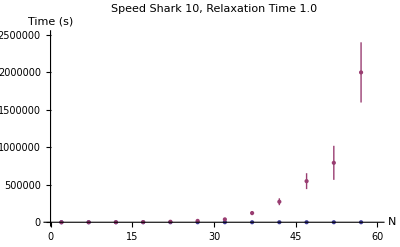

```mathematica
Needs["ErrorBarPlots`"]

dataNR={{2,38.600000,2.411904},{7,42.680000,2.232653},{12,48.155000,2.178200},{17,51.430000,1.660219},{22,60.175000,1.909609},{27,65.335000,2.864741},{32,74.030000,2.806161},{37,84.090000,2.084433},{42,88.335000,3.209501},{47,96.485000,3.049427},{52,107.975000,6.008560},{57,120.715000,7.302611}}

dataR={{2,38.105000,2.620562},{7,233.885000,28.264398},{12,811.695000,79.357315},{17,2356.080000,358.263352},{22,6717.360000,1125.404051},{27,18104.890000,2709.830933},{32,38407.470000,8033.510649},{37,122485.574998,27340.544552},{42,273137.909971,45833.062517},{47,547314.085040,105906.492432},{52,791542.065200,226712.292296},{57,1995738.934841,400936.426654}}

ErrorListPlot[{dataNR, dataR}, AxesOrigin -> {0, 0}, PlotRange -> {{0, 60.01}, {0, 2500000}}, PlotLabel -> Style["Speed Shark 10, Relaxation Time 1.0", FontSize -> 16], AxesLabel->{Style["N",FontSize->14], Style["Time (s)",FontSize->14]}]
```